1. naloga

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2= Daljica[{-1,-1},{3,1}]
d3= Daljica[{-1,2},{3,0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_,BB_]]:= Norm[BB - AA]
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]]:=Line[{AA,BB}]
ClearAll
```

ClearAll

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica]:= Graphics[Slika[d]]
```

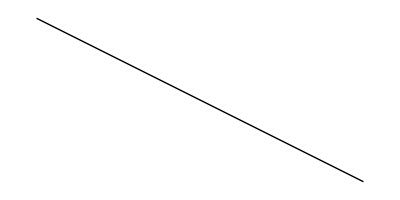

```mathematica
Narisi[d]
```

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]]:= Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
{x2,y2}=BB;
k =(y2-y1)/(x2-x1);
n = n /. First[Solve[y1==k*x1+n,n]];
y = k*x + n
]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAll
```

ClearAll

```mathematica
EnacbaNosilke[d]
```

1/2-x/2

```mathematica
y
```

1/2-x/2

2. naloga

```mathematica
v = Daljica[{-2,1},{6,-1}]
```

Daljica[{-2,1},{6,-1}]

```mathematica
ClearAll
```

ClearAll

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA+r(BB-AA) == CC+s(DD-CC),r≥0,r≤1,s≥ 0,s≤1},{r,s}];
If[resitev=={},
{},
First[AA+r(BB-AA)/.resitev]
]]
```

```mathematica
Presek[d,d3]
```

{}

```mathematica
ClearAll
```

ClearAll